#### Not Applicable If : The incident points alternate on the curve and plane mirror, there is no consecutive incidents of light on the either curve or x axis, Number of iterations limited in case of back tracing Applicable Cases: No information of source point of light, there can be multiple incidents on the same point, light can retrace its path back

Incident points input and their plot

{{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}}

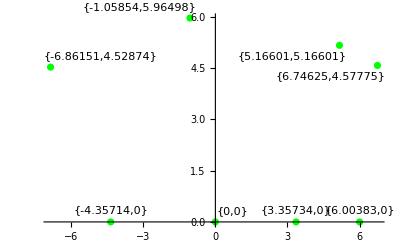

```mathematica
intersecpts = {{5.166010488516726,5.166010488516724},{6.003831069285709,0},{6.746248565974317,4.577754071440296},{3.357339206799729,0},{-1.058536173181429,5.964984411564576},{-4.357140119563605,0},{-6.861508969064321,4.528740458357809}, {0,0}}
intersecplot = ListPlot[Labeled[#,#] &/@ intersecpts, PlotRange->Full,PlotStyle->{Green}]
```

```mathematica
ExportString[intersecpts,"RawJSON","Compact"->True]
```

[[5.166010488516726,5.166010488516724],[6.003831069285709,0],[6.746248565974317,4.577754071440296],[3.357339206799729,0],[-1.058536173181429,5.964984411564576],[-4.357140119563605,0],[-6.861508969064321,4.528740458357809],[0,0]]

```mathematica
Export["C:\\Users\\PC\\Desktop\\PINN\\Python\\test.csv",intersecpts, "CSV"]
```

C:\Users\PC\Desktop\PINN\Python\test.csv

```mathematica
FilePrint["C:\\Users\\PC\\Desktop\\PINN\\Python\\test.csv"]
```

5.166010488516726,5.166010488516724
6.003831069285709,0
6.746248565974317,4.577754071440296
3.357339206799729,0
-1.058536173181429,5.964984411564576
-4.357140119563605,0
-6.861508969064321,4.528740458357809
0,0

Separate the points into x -axis (plane mirror points) and unknown reflecting curve incident points

curvepts = {{-6.86151,4.52874},{-1.05854,5.96498},{5.16601,5.16601},{6.74625,4.57775}}

xaxispts = {{-4.35714,0},{0,0},{3.35734,0},{6.00383,0}}

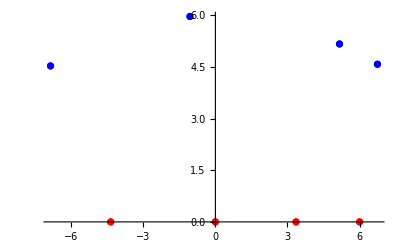

```mathematica
For[xaxispts = {}; i=0, i<Length[intersecpts], i++; If[intersecpts[[i, 2]]==0, AppendTo[xaxispts, intersecpts[[i]]]]]
curvepts = Sort[DeleteCases[intersecpts, Alternatives @@ xaxispts]];
xaxispts = Sort[xaxispts];
Print["curvepts = ", curvepts]
Print["xaxispts = ", xaxispts]
intersecplot2 = ListPlot[{#} & /@ intersecpts, PlotRange->Full,PlotStyle->{Blue, Red, Blue, Red, Blue, Red, Blue, Red}]
```

Function for initial 3 point tuple permutations

```mathematica
pttuplefunc[domainls_, codomainls_]:=
	Module[{tupleset={}},
			For[k=0, k<Length[domainls], k++;
				tupleset = AppendTo[tupleset, {domainls[[2]],codomainls[[3]], If[domainls[[k]]!={0,0}, domainls[[k]], Continue[]]}]
				];
	Return[tupleset, Module]];
```

Path permutations till the first plane mirror reflection

```mathematica
tuple3point = pttuplefunc[xaxispts, curvepts]
Print["No of tuples = ", Length[tuple3point]]
```

{{{0,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0}}}

No of tuples = 3

```mathematica
For[tupleset1 ={};k =0, k<Length[xaxispts], k++;
	For[i=0, i<Length[curvepts], i++;
		For[slope1=0, slope2 = 0;j=0, j<Length[curvepts], j++;
			If[curvepts[[i]]=curvepts[[j]], Continue[]];
			slope1 = (curvepts[[i]][[2]]-xaxispts[[k]][[2]])/(curvepts[[i]][[1]]-xaxispts[[k]][[1]]); 
			slope2 = (curvepts[[j]][[2]]-xaxispts[[k]][[2]])/(curvepts[[j]][[1]]-xaxispts[[k]][[1]]);
			Print[slope1];
			If[slope1 == -slope2, tupleset1 = AppendTo[tupleset1, {curvepts[[i]], xaxispts[[k]], curvepts[[j]]}]
			]]]];
```

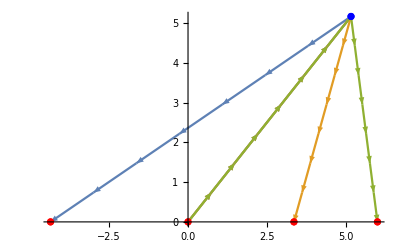

```mathematica
point3path = ListLinePlot[tuple3point, Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}] /. Line -> Arrow;
Show[point3path, intersecplot2]
```

Next we check check reflections and eliminate paths based on it

```mathematica
(*Function to check for the curve points lying on the reflected ray *)
reflecdrop[domainls_] := 
	Module[{tupleset = {}}, 
		For[i=0, i<Length[domainls], i++;
			For[(eqn = y == -(Last[List @@ Reduce[y - InterpolatingPolynomial[{Part[domainls[[i]],-2], Part[domainls[[i]],-1]},x]==0,y]]));
				j=0, j<Length[curvepts], j++;
				If[(eqn /. {x->curvepts[[j,1]], y->curvepts[[j,2]]})== True, 
					tupleset = AppendTo[tupleset,Join[domainls[[i]], {curvepts[[j]]}]]]]];
	Return[tupleset, Module]];
```

Out of 64 paths, after elimination we have 24 paths after the 1st reflection on plane mirror

```mathematica
a = reflecdrop[tuple3point];
a
```

{{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775}}}

```mathematica
path2func[path_]:= 
	Module[{tupleset={}},
		For[tupleset={};i=0, i<Length[path], i++;
			For[j=0, j<Length[xaxispts], j++;
				tupleset = Append[tupleset, Join[path[[i]], {xaxispts[[j]]}]]]; Print[tupleset]];
		Return[tupleset, Module]];
```

```mathematica
merge[list_]:=Module[{a= reflecdrop[list]}, Return[path2func[a], Module]];
function[list_]:= Module[{a, new={}},
	If[EvenQ[Length[intersecpts]]==True, a = reflecdrop[Nest[merge, list, (Length[intersecpts]-4)/2]],a = Nest[merge, list, (Length[intersecpts]-3)/2]];
	For[i=0, i<Length[a], i++;
	If[CountDistinct[a[[i]]]==Length[intersecpts], new = AppendTo[new, a[[i]]]]];
	Return[new, Module]];
```

```mathematica
finalpath = function[tuple3point][[1]]
```

{{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

{{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}}

```mathematica
7, 0, 1, 2, 3, 4, 5, 6
```

{{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}}}

```mathematica
Export["C:\\Users\\PC\\Desktop\\PINN\\Python\\correct8.csv",finalpath, "CSV"]
```

C:\Users\PC\Desktop\PINN\Python\correct8.csv

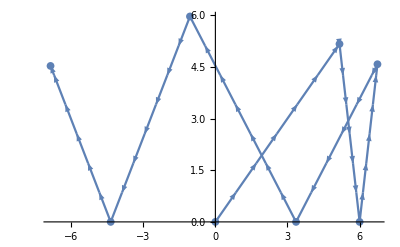

```mathematica
ListLinePlot[finalpath[[1]], PlotMarkers->{Automatic, 8}, Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}] /. Line -> Arrow
```

```mathematica
ListLinePlot[finalpath[[]], PlotMarkers->{Automatic, 8}, Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}] /. Line -> Arrow
```

Part::partw: Part 2 of {{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}}} does not exist.

Part::partw: Part 2 of {{{0.,0.},{5.16601,5.16601},{6.00383,0.},{6.74625,4.57775},{3.35734,0.},{-1.05854,5.96498},{-4.35714,0.},{-6.86151,4.52874}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: {{{0.,0.},{5.16601,5.16601},{6.00383,0.},{6.74625,4.57775},{3.35734,0.},{-1.05854,5.96498},{-4.35714,0.},{-6.86151,4.52874}}}⟦2⟧ is not a list of numbers or pairs of numbers.

ListLinePlot[{{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}}}⟦2⟧,PlotMarkers→{Automatic,8},Axes→True,AxesOrigin→{0,0},MeshFunctions→{#2&},Mesh→6,MeshStyle→Opacity[0],MeshShading→{Arrowheads[Small]},DataRange→{0,4 π}]

Comparison

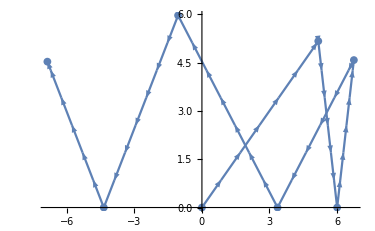
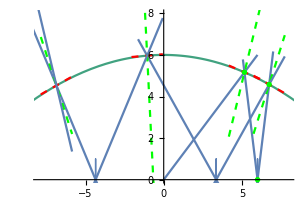

# Trying large number of iterations for back tracing

```mathematica
(* function2[list_]:= Module[{a, new={}},
	If[EvenQ[Length[intersecpts]]==True, a = reflecdrop[Nest[merge, list, 3*(Length[intersecpts]-4)/2]],a = Nest[merge, list, 3*(Length[intersecpts]-3)/2]];
	For[i=0, i<Length[a], i++;
	If[CountDistinct[a[[i]]]==Length[intersecpts], new = AppendTo[new, a[[i]]]]];
	Return[new, Module]]; *)
```

```mathematica
(* b = function2[tuple3point]*)
```

```mathematica
(* Length[b]
ListLinePlot[b, PlotMarkers->{Automatic, 8}, Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}] /. Line -> Arrow *)
```